# Nanobot Theory : Data Analysis and Plotting

#### Yibin Jiang, Abhishek Sharma Cronin Lab University of Glasgow

```mathematica
repeat = 1;
baseDirectory=NotebookDirectory[];
data=Import[baseDirectory<>"/data1/dipoles.csv"];
UVdata = Import[baseDirectory<>"/data"<>ToString[repeat]<>"/combined_data1.csv"];
```

```mathematica
dipoleLength=Quantity[0.41,"nm"];
d=QuantityMagnitude[10^-3 dipoleLength]; (* For plotting 10^-3 is a scaling factor *)
```

```mathematica
deleteIndex = 1+Flatten@IntegerPart@N@Import[baseDirectory<>"/data"<>ToString[repeat]<>"/changed_dipole_index.csv"];
position = Table[True,{i,Length@data}];
```

```mathematica
wavelength = Table[0.44+0.01i,{i,26}];
wavelength =Flatten@{wavelength,Table[0.518+0.002*i,{i,26}]};
wavelengthU = DeleteDuplicates[wavelength];
wavelengthS = 1000*Table[0.45+0.25/1000*i,{i,1000}];
wvindex = Flatten@Table[Flatten@Position[wavelength,(Sort@wavelengthU)⟦i⟧]⟦1⟧,{i,Length[wavelengthU]}];
wavelength=wavelength⟦wvindex⟧;
```

```mathematica
plotUVVis[index_]:= Block[{Au,structure,reffi,tempData,intp,plot1,plot2,fig},
position⟦deleteIndex⟦index⟧⟧ =!position⟦deleteIndex⟦index⟧⟧ ;
Au = Pick[data,position];
reffi=(3/(4π)d^3 Length@Au )^(1/3);
tempData=Transpose[{1000*wavelength,UVdata⟦All,1+index⟧/(π reffi^2)}];
intp=Interpolation[tempData,InterpolationOrder->2];
plot1=Plot[intp[x],{x,450,700},PlotStyle->Black,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotRange->{0,0.7}];
plot2=ListPlot[tempData,PlotStyle->{Black,PointSize[0.02]},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]}];
fig=Show[{plot1,plot2},PlotLabel->Style["Step: "<>ToString[index],FontSize->18],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},Frame-> True,FrameLabel->{"Wavelength (nm)","Extinction"},AspectRatio->1,ImageSize->300,PlotRange->{0,0.7}];
{fig}]
```

```mathematica
Dimensions@wavelength
```

{46}

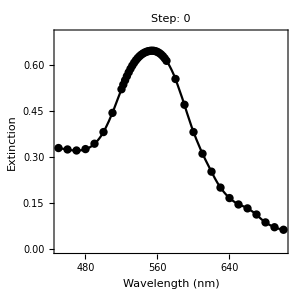

/mnt/orkney1/Chemobot/Nanobot-Monte_Carlo_Simulation/Monte_Carlo_Exp//plots1/Uv0.png

```mathematica
index = 0;
Au = data;
reffi=(3/(4π)d^3 Length@Au )^(1/3);
tempData=Transpose[{1000*wavelength,UVdata⟦All,1+index⟧/(π reffi^2)}];
intp=Interpolation[tempData,InterpolationOrder->2];
plot1=Plot[intp[x],{x,450,700},PlotStyle->Black,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotRange->{0,0.7}];
plot2=ListPlot[tempData,PlotStyle->{Black,PointSize[0.02]},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]}];
fig=Show[{plot1,plot2},PlotLabel->Style["Step: "<>ToString[index],FontSize->18],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},Frame-> True,FrameLabel->{"Wavelength (nm)","Extinction"},AspectRatio->1,ImageSize->300,PlotRange->{0,0.7}];
p1 = fig
Export[baseDirectory<>"/plots1/Uv"<>ToString[index]<>".png",p1,ImageResolution-> 300]
```

```mathematica
Table[
p1=plotUVVis[index]⟦1⟧;
Export[baseDirectory<>"/plots1/Uv"<>ToString[index]<>".png",p1,ImageResolution-> 300],{index,1,Length[deleteIndex]}]
```

{/mnt/orkney1/Chemobot/Nanobot-Monte_Carlo_Simulation/Monte_Carlo_Exp//plots1/Uv1.png,/mnt/orkney1/Chemobot/Nanobot-Monte_Carlo_Simulation/Monte_Carlo_Exp//plots1/Uv2.png,14771,/mnt/orkney1/Chemobot/Nanobot-Monte_Carlo_Simulation/Monte_Carlo_Exp//plots1/Uv14774.png}
 |  |  |  |